```mathematica
2+3
```

5

```mathematica
(2+3)*2^5+a b^3
```

160+a b^3

```mathematica
Expand[(x+1)(x+2)(x+3)]
```

6+11 x+6 x^2+x^3

```mathematica
Solve[x^3+4x-4==0,x]
```

{{x→Root0.848Root[-4+4 #1+#1^3&,1]0.8477075981395665},{x→Root-0.424-2.13 ⅈRoot[-4+4 #1+#1^3&,2]-0.4238537990697833},{x→Root-0.424+2.13 ⅈRoot[-4+4 #1+#1^3&,3]-0.4238537990697833}}

```mathematica
Solve[a x^3+b x+c x+d==0,x]//ToRadicals
```

{{x→-(2^(1/3) (b+c))/((-27 a^2 d+√(108 a^3 (b+c)^3+729 a^4 d^2))^(1/3))+((-27 a^2 d+√(108 a^3 (b+c)^3+729 a^4 d^2))^(1/3))/(3 2^(1/3) a)},{x→((1+ⅈ √3) (b+c))/(2^(2/3) (-27 a^2 d+√(108 a^3 (b+c)^3+729 a^4 d^2))^(1/3))-((1-ⅈ √3) (-27 a^2 d+√(108 a^3 (b+c)^3+729 a^4 d^2))^(1/3))/(6 2^(1/3) a)},{x→((1-ⅈ √3) (b+c))/(2^(2/3) (-27 a^2 d+√(108 a^3 (b+c)^3+729 a^4 d^2))^(1/3))-((1+ⅈ √3) (-27 a^2 d+√(108 a^3 (b+c)^3+729 a^4 d^2))^(1/3))/(6 2^(1/3) a)}}

```mathematica
Limit[(Sum[1/k,{k,1,n}]),n->Infinity]
```

∞

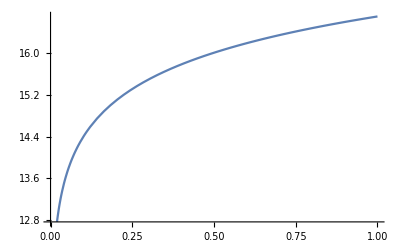

```mathematica
Plot[Sum[1/i, {i, 1, n}], {n, 1, 10000000}]
```

```mathematica
Limit[(Sum[1/k,{k,1,n}]-Log[n]),n->Infinity]
```

EulerGamma

```mathematica
fb[0]=1
```

1

```mathematica
fb[1]=1
```

1

```mathematica
fb[n_]:=fb[n-1]+fb[n-2];
```

```mathematica
fb[3]
```

2

```mathematica
f[x_, y_] := x + y /; (x ~ Element ~ Reals && y ~ Element ~ Reals)
```

```mathematica
A={-a,0};B={a,0};G={0,1};Solve[{(G-A).(B-G)==8,a>1}]

lineq[{x1_,y1_},{x2_,y2_}]:=FullSimplify[(y-y1)*(x2-x1)-(x-x1)*(y2-y1)==0];
a=3;P={6,p};c={x,y}/. First@Solve[{x^2/9+y^2==1,lineq[P,A],y≠0},{x,y}];
d={x,y}/. First@Solve[{x^2/9+y^2==1,lineq[P,B],y≠0},{x,y}];
lineq[c,d]
```

{{a→3}}

((3+p^2) (-9 y+p (-6+4 x+3 p y)))/((1+p^2) (9+p^2))==0